```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/armin/my_programs/alphaLoopMisc/graph_generation/example

```mathematica
<<"../orientedGraphTools.m"
```

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs
 ----------------------------------------- 
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation

```mathematica
(* Load ggHH 2 Loop graphs *)
```

```mathematica
allGraphs=ToExpression["{"<>StringDrop[StringReplace[Import["ggHH.qgr","Text"],{"**NewDiagram**"->",","\n"->""}]<>"}",1]];
```

```mathematica
exampleGraphs=allGraphs[[2;;3]]
```

{{factor2→-1,{{in1→5,in[gluon[p1]]},{in2→5,in[gluon[p2]]},{1→out1,out[higgs[p3]]},{2→out2,out[higgs[p4]]},{1→2,t[-k1]},{3→1,t[-k1-p3]},{2→4,t[-k1+p4]},{4→3,t[k2]},{3→5,gluon[k1+k2+p3]},{4→5,gluon[-k1-k2+p4]}}},{factor3→-1,{{in1→5,in[gluon[p1]]},{in2→5,in[gluon[p2]]},{1→out1,out[higgs[p3]]},{2→out2,out[higgs[p4]]},{2→1,t[k1]},{1→3,t[k1+p3]},{4→2,t[k1-p4]},{3→4,t[-k2]},{3→5,gluon[k1+k2+p3]},{4→5,gluon[-k1-k2+p4]}}}}

```mathematica
(* Lets plot some isomorphic graphs *)
```

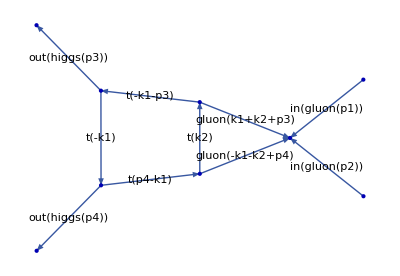

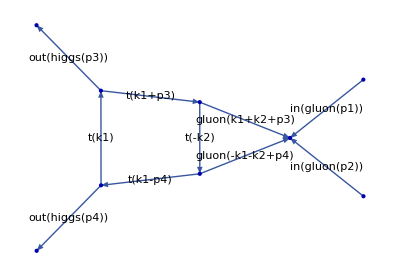

```mathematica
plotGraph[#,Scaled[0.3]]&/@(exampleGraphs[[All,2]]);
```

```mathematica
(* find the isomorphism *)
```

```mathematica
(* translate labels to taggings, but we can also add taggings if we have cuts or complex conjugation *)
```

```mathematica
taggedExample=exampleGraphs[[All,2]]/. in[f_[x_]]:>x/. out[f_[x_]]:>x /. gluon[x__]:> mg /. t[x__]:>mt /. {Rule[a_,b_],x_}:>{Rule[a,b],{x}};
```

```mathematica
findIsomorphicGraphs[taggedExample]
```

{{{2,1},{{<|1→1,2→2,3→3,out1→out1,4→4,out2→out2,5→5,in1→in1,in2→in2|>,Cycles[{}],{1,1,1,1,-1,-1,-1,-1,1,1}}}}}